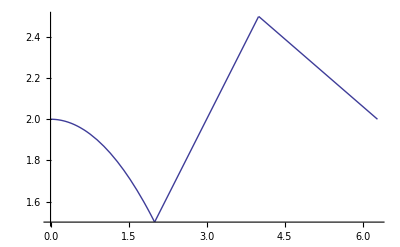

```mathematica
f[x_]:=Piecewise[{{1-0.5 x^2,0≤ x<1},{x-0.5,1≤x<2},{0.5(x-π)/(2-π)+1,2≤ x≤ π}}]+1
Plot[f[x/2],{x,0,2π}]
```

```mathematica
Cn=Table[1/π NIntegrate[f[x/2] Cos[n x],{x,0,2π}],{n,0,20}]
Sn=Table[1/π NIntegrate[f[x/2] Sin[n x],{x,0,2π}],{n,1,20}]
```

{4.07559,-0.0144786,0.0187355,-0.0210694,-0.0139302,0.0112845,-0.00689868,-0.00657704,0.00661224,-0.003899,-0.00344976,0.00394506,-0.00248082,-0.00182404,0.00221178,-0.00152009,-0.000948535,0.00105055,-0.000786195,-0.000509189,0.000300717}

{-0.349949,0.13328,-0.0036449,-0.0223765,0.016455,-0.00095515,-0.00496951,0.00370807,0.00018604,-0.00115361,0.00017634,0.000807281,-0.0000873766,-0.000992039,0.00110768,0.000140075,-0.00126388,0.00116904,0.0000980938,-0.00114502}

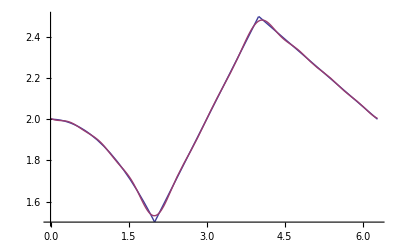

```mathematica
Plot[{f[x/2],Evaluate[Sum[Cn[[i+1]]Cos[i x]+Sn[[i]]Sin[i x],{i,1,10}]]+Cn[[1]]/2},{x,0,2π},PlotRange->All]
```

```mathematica
fmod[x_]:=2*π*SawtoothWave[x/2/π]
```

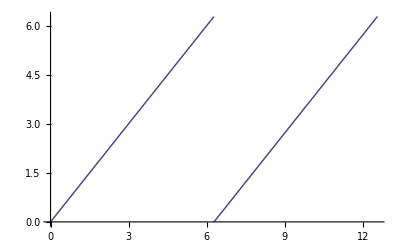

```mathematica
Plot[2π SawtoothWave[x/(2π)],{x,0,4π}]
```

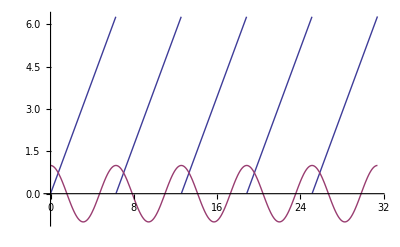

```mathematica
Plot[{fmod[x],Cos[x]},{x,0,10π}]
```

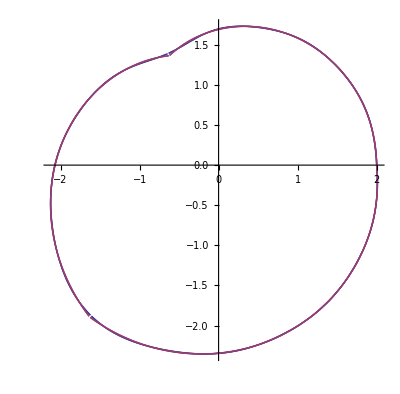

```mathematica
PolarPlot[{
(Sum[Cn[[i+1]]Cos[i x]+Sn[[i]]Sin[i x],{i,1,10}]+Cn[[1]]/2),
f[fmod[x]/2]
(*f[fmod[x]/2]+1,
f[fmod[x]/2]-1*)
},{x,0,4π}]
```

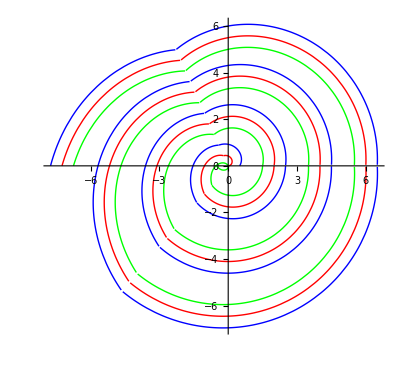

```mathematica
PolarPlot[{
(*(Sum[Cn[[i+1]]Cos[i x]+Sn[[i]]Sin[i x],{i,1,10}]+Cn[[1]]/2)x/(2π),*)
f[fmod[x]/2] x/(2π),
(f[fmod[x]/2])x/(2π)+0.5,
(f[fmod[x]/2])x/(2π)-0.5
},{x,0,7π},PlotStyle->{Red,Blue,Green},PlotPoints->50]
```